## Initialisation : 2 Spheres - 1 Link swimmer.

```mathematica
ClearAll["Global`*"];
x12 = L;

λ12 = R1 / x12;
λ21 = R2 / x12;

A11 = A22 = B11 = B22 = 1;
A12  = 3/2 λ12;
A21  = 3/2 λ21;
B12  = 3/4 λ12;
B21  = 3/4 λ21;

mob1 = 1/(6 π μ R1);
mob2 =1/(6 π μ R2);

n = {1, 0, 0};
nn = Outer[Times, n, n];
Imnn = IdentityMatrix[3] - nn;

H11 = mob1 (A11 nn + B11 Imnn);
H22 = mob2 (A22 nn + B22 Imnn);
H12 =mob1 (A12 nn + B12 Imnn);
H21 =mob2 (A21 nn + B21 Imnn);

Fv1 = {f1, 0, 0};
Fv2 = {f2, 0, 0};

v1 = (H11.Fv1 + H12.Fv2)[[1]] /. f2-> -f1;
v2 = (H21.Fv1 + H22.Fv2)[[1]] /. f2-> -f1;
vs = (v1 + v2)/2;

Ldot = v2 - v1;

f1solved = (Solve[Ldot == LDOT, {f1}] // Flatten)[[1, 2]] // Simplify;
f2solved = - f1solved;

v1solved = v1/. {f1 -> f1solved} // Simplify;
v2solved = v2/. {f1 -> f1solved} // Simplify;
vssolved = vs/. {f1 -> f1solved} // Simplify;
```

## Harmonic Deformations, defining

```mathematica
L = l (1 + e Cos[ω t + ϕ]);
LDOT = D[L, t];
vssolved
```

-(e l^2 (R1-R2) ω (1+e Cos[ϕ+t ω]) Sin[ϕ+t ω])/(-6 R1 R2+2 l (R1+R2) (1+e Cos[ϕ+t ω]))

## Non-Dimensionalized

```mathematica
V1 = Collect[v1solved/. {R1 -> α R2, l -> x R2, t-> T/ω}, {R2, ω}]//Simplify;
V2 = Collect[v2solved/. {R1 -> α R2, l -> x R2, t-> T/ω}, {R2, ω}]//Simplify;
VS = Collect[vssolved/. {R1 -> α R2, l -> x R2, t-> T/ω}, {R2, ω}]//Simplify;
F1 = Collect[ f1solved/. {R1 -> α R2, l -> x R2, t-> T/ω}, {R2, ω, μ}]//Simplify;
F2 = Collect[ f2solved/. {R1 -> α R2, l -> x R2, t-> T/ω}, {R2, ω, μ}]//Simplify;
Lstar= Collect[ L/. {R1 -> α R2, l -> x R2, t-> T/ω}, {R2, ω}]//Simplify;
Ldotstar = Collect[ LDOT/. {R1 -> α R2, l -> x R2, t-> T/ω}, {R2, ω}]//Simplify;
```

## Analysis of Displacement

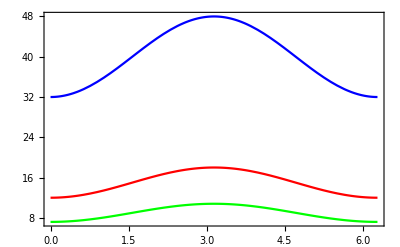

```mathematica
Show[
Plot[Lstar /. {α -> 1, x -> 40, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π}, Frame-> True, PlotRange->All, PlotStyle->{Blue}]
,
Plot[Lstar /. {α -> 1, x -> 15, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π}, Frame-> True, PlotRange->All, PlotStyle->{Red}]
,
Plot[Lstar /. {α -> 1, x -> 9, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π}, Frame-> True, PlotRange->All, PlotStyle->{Green}]
]
```

```mathematica
Clear[Δs, Δ1, Δ2, V1DATA, V2DATA, VSDATA, F1DATA, F2DATA];
X = 5;
ALPHA = 2;
Δs = Table[ NIntegrate[VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ1 = Table[ NIntegrate[V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ2 = Table[ NIntegrate[V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
V1DATA = Table[ V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
V2DATA = Table[ V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
VSDATA = Table[ VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
F1DATA = Table[ F1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
F2DATA = Table[ F2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
```

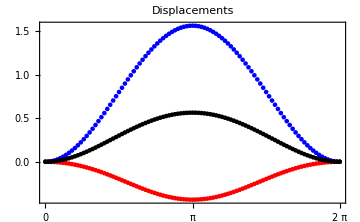
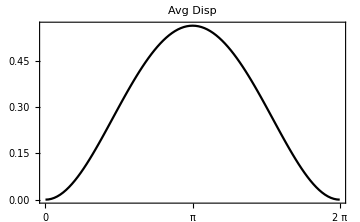
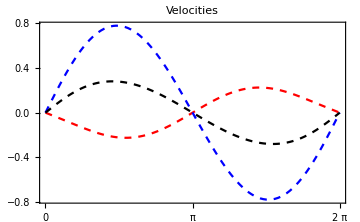
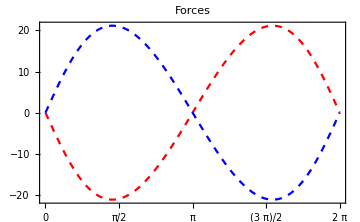

```mathematica
{
Show[ListPlot[Δ1, DataRange->{0, 2π}, PlotStyle-> Red], ListPlot[Δ2, DataRange->{0,2π}, PlotStyle-> Blue],ListPlot[Δs, DataRange->{0,2π}, PlotStyle-> Black], PlotRange-> All, Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Displacements",ImageSize->Medium]
,
ListLinePlot[Δs, DataRange->{0,2π}, PlotStyle-> Black,Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Avg Disp",ImageSize->Medium]
,
Show[
ListLinePlot[V1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[V2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
ListLinePlot[VSDATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Black}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Velocities",ImageSize->Medium, PlotRange -> All]
,
Show[
ListLinePlot[F1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[F2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/2, Pi,3 Pi/2,2Pi},None}},PlotLabel->"Forces",ImageSize->Medium, PlotRange -> All]
}
```

```mathematica
Clear[Δs, Δ1, Δ2, V1DATA, V2DATA, VSDATA, F1DATA, F2DATA];
X = 5;
ALPHA = 3;
Δs = Table[ NIntegrate[VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ1 = Table[ NIntegrate[V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ2 = Table[ NIntegrate[V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
V1DATA = Table[ V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
V2DATA = Table[ V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
VSDATA = Table[ VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
F1DATA = Table[ F1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
F2DATA = Table[ F2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
```

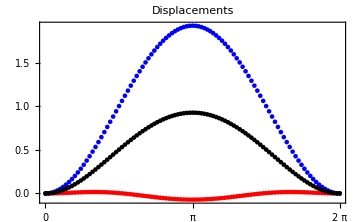
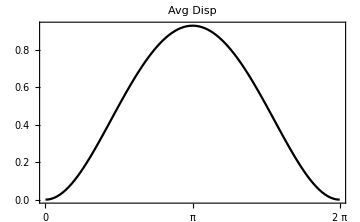
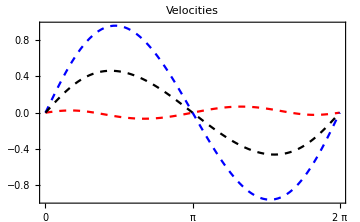
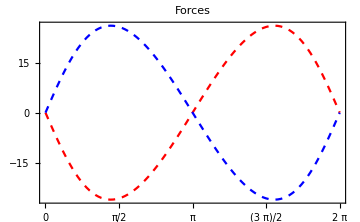

```mathematica
{
Show[ListPlot[Δ1, DataRange->{0, 2π}, PlotStyle-> Red], ListPlot[Δ2, DataRange->{0,2π}, PlotStyle-> Blue],ListPlot[Δs, DataRange->{0,2π}, PlotStyle-> Black], PlotRange-> All, Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Displacements",ImageSize->Medium]
,
ListLinePlot[Δs, DataRange->{0,2π}, PlotStyle-> Black,Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Avg Disp",ImageSize->Medium]
,
Show[
ListLinePlot[V1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[V2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
ListLinePlot[VSDATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Black}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Velocities",ImageSize->Medium, PlotRange -> All]
,
Show[
ListLinePlot[F1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[F2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/2, Pi,3 Pi/2,2Pi},None}},PlotLabel->"Forces",ImageSize->Medium, PlotRange -> All]
}
```

```mathematica
Clear[Δs, Δ1, Δ2, V1DATA, V2DATA, VSDATA, F1DATA, F2DATA];
X = 5;
ALPHA = 5;
Δs = Table[ NIntegrate[VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ1 = Table[ NIntegrate[V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ2 = Table[ NIntegrate[V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
V1DATA = Table[ V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
V2DATA = Table[ V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
VSDATA = Table[ VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
F1DATA = Table[ F1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
F2DATA = Table[ F2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
```

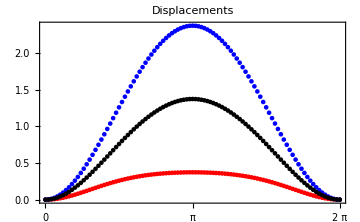
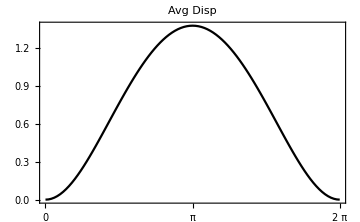
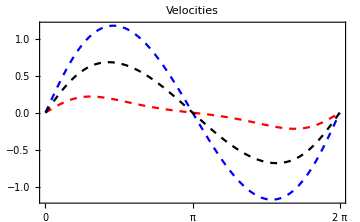
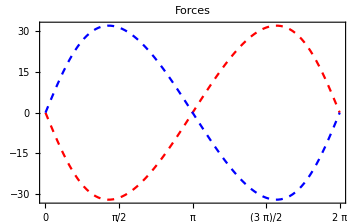

```mathematica
{
Show[ListPlot[Δ1, DataRange->{0, 2π}, PlotStyle-> Red], ListPlot[Δ2, DataRange->{0,2π}, PlotStyle-> Blue],ListPlot[Δs, DataRange->{0,2π}, PlotStyle-> Black], PlotRange-> All, Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Displacements",ImageSize->Medium]
,
ListLinePlot[Δs, DataRange->{0,2π}, PlotStyle-> Black,Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Avg Disp",ImageSize->Medium]
,
Show[
ListLinePlot[V1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[V2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
ListLinePlot[VSDATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Black}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Velocities",ImageSize->Medium, PlotRange -> All]
,
Show[
ListLinePlot[F1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[F2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/2, Pi,3 Pi/2,2Pi},None}},PlotLabel->"Forces",ImageSize->Medium, PlotRange -> All]
}
```

```mathematica
Clear[Δs, Δ1, Δ2, V1DATA, V2DATA, VSDATA, F1DATA, F2DATA];
X = 6;
ALPHA = 3;
Δs = Table[ NIntegrate[VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ1 = Table[ NIntegrate[V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ2 = Table[ NIntegrate[V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
V1DATA = Table[ V1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
V2DATA = Table[ V2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
VSDATA = Table[ VS /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1}, {T, 0, 2π, 2π/100}];
F1DATA = Table[ F1 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
F2DATA = Table[ F2 /. {α -> ALPHA, x -> X, e-> 0.2, ω -> 1, ϕ -> π, R2-> 1, μ -> 1}, {T, 0, 2π, 2π/100}];
```

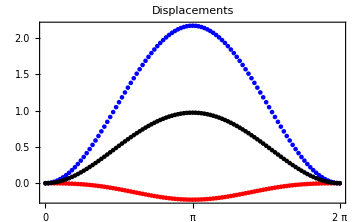
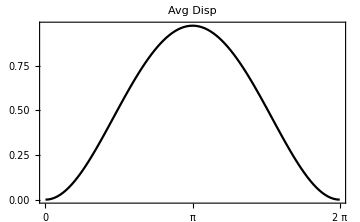
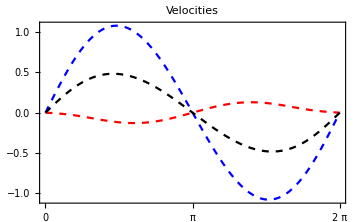
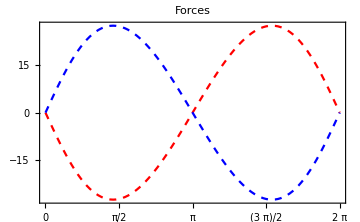

```mathematica
{
Show[ListPlot[Δ1, DataRange->{0, 2π}, PlotStyle-> Red], ListPlot[Δ2, DataRange->{0,2π}, PlotStyle-> Blue],ListPlot[Δs, DataRange->{0,2π}, PlotStyle-> Black], PlotRange-> All, Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Displacements",ImageSize->Medium]
,
ListLinePlot[Δs, DataRange->{0,2π}, PlotStyle-> Black,Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Avg Disp",ImageSize->Medium]
,
Show[
ListLinePlot[V1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[V2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
ListLinePlot[VSDATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Black}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi,2Pi},None}},PlotLabel->"Velocities",ImageSize->Medium, PlotRange -> All]
,
Show[
ListLinePlot[F1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[F2DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Blue}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/2, Pi,3 Pi/2,2Pi},None}},PlotLabel->"Forces",ImageSize->Medium, PlotRange -> All]
}
```